```mathematica
(*Dawid Bitner*)
(*moduł 3*)
(*zad 1*)
Metropolis[f_, x0_, t_, mT_, R_]:=Module[{xb, x, y,yn, yb, n, i, e, r},
(* na początku najlepsze roziwązanie to te bieżące *)
xb = x0;
x = x0;
(* określenie jakości rozwiązania *)
y = f[x[[1]],x[[2]]];
yb = y;
	
Do[
(* generujemy sąsiedztwo *)n = {RandomReal[{x[[1]]-R,x[[1]]+R}],RandomReal[{x[[2]]-R,x[[2]]+R}]};
(* określamy jego jakość *)
yn = f[n[[1]],n[[2]]];
(* energia cząsteczki *)
e = y - yn;
(* sprawdzamy czy energia jest mniejsza od 0 *)
If[e < 0,
(* jeśli tak to sprawdź to przypisanie x' jako punktu bieżącego *)
x= n ;
y = f[x[[1]],x[[2]]];
(* jeżeli punkt ten jest lepszy to przypsiz do najlepszego *)
If[y<yb,
xb = x;
yb = y;
],
(* jeżeli energia jest większa od 0 to losujemy równomierny przedział (0,1) *)
r = RandomReal[{0,1}];
(* jeśli wylosowana liczba jest mniejsza od e[-e/t] to ... *)
If[r<Exp[-e/t],
x= n;
]]
,{i,1,mT}];
Print["Najlepsze x: ", xb, "Najlepsze f(x):", yb];
];
```

```mathematica
(*zad 2*)
Algorytm[f_, x0_, t0_, mT_, R_, tN_]:=Module[{xb, x, y,yn, yb, n, i, e, r, t},
xb = x0;
x = x0;
(* określenie jakości rozwiązania *)
y = f[x[[1]],x[[2]]];
yb = y;
	
(* wybór temperatury początkowej *)
t=t0;
For[i=1, i<mT, i++,
(* generowanie sąsiedztwa *)n = {RandomReal[{x[[1]]-R,x[[1]]+R}],RandomReal[{x[[2]]-R,x[[2]]+R}]};
(* określenie jakości sąsiedztwa *)
yn = f[n[[1]],n[[2]]];
(*Energia cząsteczki*)
e = y - yn;
(* sprawdzamy czy energia jest mniejsza od 0 *)
If[e < 0,
(* jak tak to sprawdź to przypisanie x' jako punktu bieżącego *)
x= n ;
y = f[x[[1]],x[[2]]];
(* jeżeli punkt ten jest lepszy to przypsiz do najlepszego *)
If[y<yb,
xb = x;
yb = y;
],
(* jeżeli energia jest większa od 0 to losujemy równomierny przedział (0,1) *)
r = RandomReal[{0,1}];
(* jeśli wylosowana liczba jest mniejsza od e[-e/t] to ... *)
If[r<Exp[-e/t],
x= n;
]]
(* wychładzanie *)
t==t0*i*((t0-tN)/tN);
];
Print["Najlepsze x: ", xb, "Najlpsze f(x): ", yb];
];
```

```mathematica
(*zad 3*)
Ackley[x_,y_]= -20Exp[-0.2*Sqrt[0.5*(x^2+y^2)]]-Exp[0.5*(Cos[2*Pi*x]+Cos[2*Pi*y])]+E+20;
Rosenbrock[x_,y_]= 100*(y-x^2)^2 + (1-x)^2;
Algorytm[Ackley,{1,1}, 1, 50, 0.5, 0.1]
Algorytm[Rosenbrock,{1,1}, 1, 50, 0.5, 0.1]
Metropolis[Ackley, {1,1}, 1, 50, 0.5]
Metropolis[Rosenbrock, {1,1}, 1, 50, 0.5]
(* algorytm ze zmienną temperaturą znajduje lepsze roziwązania *)
```

Najlepsze x: {1,1}Najlpsze f(x): 3.62538

Najlepsze x: {1,1}Najlpsze f(x): 0

Najlepsze x: {1,1}Najlepsze f(x):3.62538

Najlepsze x: {1,1}Najlepsze f(x):0

```mathematica
(*zad4*)
(* via https://platforma.polsl.pl/rms/pluginfile.php/93065/mod_resource/content/1/Zach%C5%82anny%20i%20wy%C5%BCarzanie.pdf *)
Schema1[t0_, tN_, max_]:=Module[{t, i, tn={}},
t=t0;
AppendTo[tn, t];
For[i=1, i<max,i++,
(* jeden z przykładów schematów chłodzenia *)
t=t0*i*((t0-tN)/tN);
AppendTo[tn, t];
];
Print[ListPlot[tn]];
];
Schema2[t0_, tN_, max_]:=Module[{t, i, a, tn={}},
t=t0;
AppendTo[tn, t];
For[i=1, i<max,i++,
(* jeden z przykładów schematów chłodzenia *)
a=((t0-tN)*(max+1))/max;
t=(a/(i+1))+t0-a;
AppendTo[tn, t];
];
Print[ListPlot[tn]];
];

Schema3[t0_, tN_, max_]:=Module[{t, i, tn={}},
t=t0;
AppendTo[tn, t];
For[i=1, i<max,i++,
(* jeden z przykładów schematów chłodzenia *)
t=t0*(tN/t0)^(1/max);
AppendTo[tn, t];
];
Print[ListPlot[tn]];
];
```

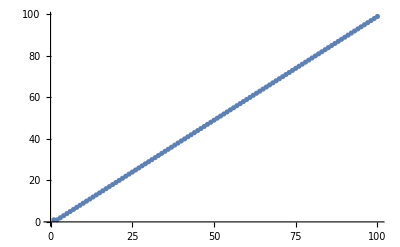

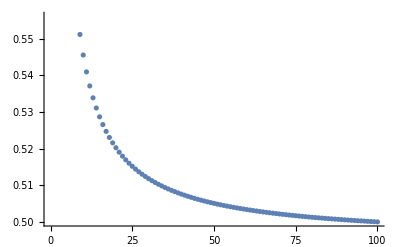

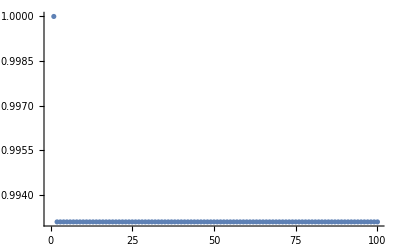

```mathematica
Schema1[1,0.5,100]
Schema2[1,0.5,100]
Schema3[1,0.5,100]
```